### functions

#### parts

```mathematica
randomEIConnectivity[totN_,eR_,means_,gains_]:=If[Or[eR==0,eR==1],
Table[RandomVariate[NormalDistribution[means,gains/Sqrt[totN]],totN],totN],
Module[{eN=Round[eR*totN],iN,meanEE,meanEI,meanIE,meanII},
iN=totN-eN;
If[Length[means]==1,
meanEE=means[[1]];meanEI=-meanEE*eN/iN;meanIE=meanEE;meanII=meanEI,
If[Length[means]==2,
meanEE=means[[1]];meanEI=-meanEE*eN/iN;meanIE=means[[2]];meanII=-meanIE*eN/iN,
If[Length[means]==4,
meanEE=means[[1]];meanEI=means[[2]];meanIE=means[[3]];meanII=means[[4]],]]];
Return[ArrayFlatten[{{Table[RandomVariate[NormalDistribution[meanEE,gains[[1,1]]/Sqrt[(*eN*)totN]],eN],eN],Table[RandomVariate[NormalDistribution[meanEI,gains[[1,2]]/Sqrt[(*iN*)totN]],iN],eN]},{Table[RandomVariate[NormalDistribution[meanIE,gains[[2,1]]/Sqrt[(*eN*)totN]],eN],iN],Table[RandomVariate[NormalDistribution[meanII,gains[[2,2]]/Sqrt[(*iN*)totN]],iN],iN]}}]]]]
randomExternalConnectivity[totN_,popRs_,externalInputRs_]:=Apply[Join,Table[RandomVariate[BernoulliDistribution[externalInputRs[[popIdx]]],Ceiling[popRs[[popIdx]]*totN]],{popIdx,Length[popRs]}]][[1;;totN]];
```

```mathematica
indicator[internalLabeled_,x_]:=internalLabeled[[2]]*(Sign[Ramp[x-internalLabeled[[1,1]]]]-Sign[Ramp[x-internalLabeled[[1,2]]]])
```

```mathematica
rk4OdeSolver[velocities_,initials_,domain_,resolution_]:=Module[{positionsOutput=Table[Table[0,Length[initials]],(domain[[2]]-domain[[1]])*resolution+1],positionsPresent=initials,positionsNext,correction1,correction2,correction3,correction4,stepSize=1/resolution},
positionsOutput[[1]]=initials;
Do[correction1=velocities[positionsPresent];
correction2=velocities[positionsPresent+stepSize*correction1/2];
correction3=velocities[positionsPresent+stepSize*correction2/2];
correction4=velocities[positionsPresent+stepSize*correction3];
positionsNext=positionsPresent+stepSize*(correction1/6+correction2/3+correction3/3+correction4/6);
positionsOutput[[idx+1]]=positionsNext;
positionsPresent=positionsNext,
{idx,(domain[[2]]-domain[[1]])*resolution}];
positionsOutput=Transpose[positionsOutput];
Return[positionsOutput]
]
rk4OdeXSolver[velocities_,externals_,initials_,domain_,resolution_]:=
Module[{velocities4,initials4,dimN=Length[initials]},
velocities4[positions4_]:=Join[velocities[positions4[[1;;dimN]]]+externals[positions4[[dimN+1]]],{1}];
initials4=Join[initials,{domain[[1]]}];
Return[rk4OdeSolver[velocities4,initials4,domain,resolution][[1;;dimN]]]]
rk4OdeXSolverSegmenting[velocities_,externals_,initials_,domains_,resolution_]:=Module[{positions=Table[Table[Table[0,(domains[[domainIdx,2]]-domains[[domainIdx,1]])*resolution+1],Length[externals]],{domainIdx,Length[domains]}],initialsT=initials},
Do[positions[[domainIdx]]=rk4OdeXSolver[velocities,externals,initialsT,domains[[domainIdx]],resolution];initialsT=Last[Transpose[positions[[domainIdx]]]](*positionsT[[;;,(domains[[domainIdx,2]]-domains[[domainIdx,1]])*resolution+1]]*),{domainIdx,Length[domains]}];
Return[positions]]
```

```mathematica
(*crossCorrelationMoment[list1_,list2_,lag_]:=list1[[1;;Length[list1]-lag]].list2[[lag+1;;Length[list2]]]/Norm[list1]/Norm[list2]
crossCorrelationCumulant[list1_,list2_,lag_]:=Module[{mean1=Mean[list1],mean2=Mean[list2]},Return[(list1[[1;;Length[list1]-lag]]-mean1).(list2[[lag+1;;Length[list2]]]-mean2)/Norm[list1-mean1]/Norm[list2-mean2]]]*)
crossCorrelationMoment[list1_,list2_,lag_]:=Mean[list1[[1;;Length[list1]-lag]]*list2[[lag+1;;Length[list2]]]]/Sqrt[Mean[Abs[list1]^2]]/Sqrt[Mean[Abs[list2]^2]]
crossCorrelationCumulant[list1_,list2_,lag_]:=Module[{mean1=Mean[list1],mean2=Mean[list2]},Return[Mean[(list1[[1;;Length[list1]-lag]]-mean1)*(list2[[lag+1;;Length[list2]]]-mean2)]/Sqrt[Mean[Abs[list1-mean1]^2]]/Sqrt[Mean[Abs[list2-mean2]^2]]]]
(*With[{foo=Table[Exp[-idx],{idx,0,10}]},
ListPlot[{Table[{lag,crossCorrelationMoment[foo,foo,lag]},{lag,0,10}],Table[{lag,crossCorrelationCumulant[foo,foo,lag]},{lag,0,10}]}]]*)
```

```mathematica
participationRatio[list_]:=Mean[list]^2/Mean[list^2]
```

```mathematica
save[expression_,filename_]:=Module[{imported},Export[StringJoin[NotebookDirectory[],filename,".mx"],expression];imported=Import[StringJoin[NotebookDirectory[],filename,".mx"]];
If[imported==expression,Print[StringJoin["saved to ",filename]]]]
```

```mathematica
firstPcSimilarity[cov1_,cov2_]:=Module[{ev1=First[Eigenvectors[cov1]],ev2=First[Eigenvectors[cov2]]},ev1.ev2/Norm[ev1]/Norm[ev2]]
overlapSimilarity[cov1_,cov2_]:=Norm[(DiagonalMatrix[Sqrt[Eigenvalues[cov1]]].Eigenvectors[cov1]).Transpose[DiagonalMatrix[Sqrt[Eigenvalues[cov2]]].Eigenvectors[cov2]],"Frobenius"](*/Sqrt[Tr[cov1]]/Sqrt[Tr[cov2]]*)
```

#### simulations

```mathematica
randomEIRateSimulations[connectivityParameters_,externalConnectivityParameters_,externalInputParameters_,initialConditionParameters_,simulationParameters_]:=Module[{connectivitys=Table[Apply[randomEIConnectivity,connectivityParameters[[2]]],connectivityParameters[[1]]],externalConnectivitys,phases,waves=externalInputParameters[[2]],initialConditions,labeledTimeIs=simulationParameters[[1]],resolution=simulationParameters[[2]],totN=connectivityParameters[[2,1]],stateStats,acs,covs,prsPca,prsEv,prsNatural,sampleStateTraces,rotationEv,nonlinearity1=Identity,nonlinearity2=Tanh,velocities,externals,stateTrace,stateT,covT},
(*********)
externalConnectivitys=Table[Apply[randomExternalConnectivity,Join[{totN},externalConnectivityParameters[[2]]]],externalConnectivityParameters[[1]]];
phases=Table[Exp[2Pi*I*RandomVariate[UniformDistribution[{0,1}],totN]],externalInputParameters[[1]]];
If[Dimensions[initialConditionParameters[[2]]]=={totN},initialConditions=Table[initialConditionParameters[[2]],initialConditionParameters[[1]]],If[Dimensions[initialConditionParameters[[2]]]=={totN,totN},
initialConditions=ArcTanh[RandomVariate[Apply[MultinormalDistribution,initialConditionParameters[[2]]],initialConditionParameters[[1]]]],
initialConditions=Table[Table[Table[0,totN],initialConditionParameters[[1]]],connectivityParameters[[1]]];
Do[velocities[positions_]:=-positions+nonlinearity1[connectivitys[[connectivityIdx]].nonlinearity2[positions]];
externals[positions_]:=0;
stateT=Last[rk4OdeXSolverSegmenting[velocities,externals,RandomVariate[NormalDistribution[0,1],totN],labeledTimeIs[[;;,1]],resolution]];
covT=stateT.Transpose[stateT];
initialConditions[[connectivityIdx]]=ArcTanh[RandomVariate[Apply[MultinormalDistribution,{Table[0,totN],covT}],initialConditionParameters[[1]]]],{connectivityIdx,connectivityParameters[[1]]}]],];
Print[Grid[Transpose[{{"connectivityN","externalConnectivityN","phaseN","waveN","initialConditionN","labeledTimeIN"},{connectivityParameters[[1]],externalConnectivityParameters[[1]],externalInputParameters[[1]],Length[waves],Length[initialConditions],Length[labeledTimeIs]}}]]];
(*********)
stateStats=Table[Table[Table[Table[Table[Table[{0,0},{timeIIdx,Length[labeledTimeIs]}],{initialConditionIdx,Length[initialConditions]}],{waveIdx,Length[waves]}],{phaseIdx,externalInputParameters[[1]]}],{externalConnectivityIdx,externalConnectivityParameters[[1]]}],{connectivityIdx,connectivityParameters[[1]]}];
acs=Table[Table[Table[Table[Table[Table[Table[{lag,0},{lag,0,labeledTimeIs[[timeIIdx,1,2]]-labeledTimeIs[[timeIIdx,1,1]],1}],{timeIIdx,Length[labeledTimeIs]}],{initialConditionIdx,Length[initialConditions]}],{waveIdx,Length[waves]}],{phaseIdx,externalInputParameters[[1]]}],{externalConnectivityIdx,externalConnectivityParameters[[1]]}],{connectivityIdx,connectivityParameters[[1]]}];
covs=Table[Table[Table[Table[Table[Table[Table[Table[0,totN],totN],{timeIIdx,Length[labeledTimeIs]}],{initialConditionIdx,Length[initialConditions]}],{waveIdx,Length[waves]}],{phaseIdx,externalInputParameters[[1]]}],{externalConnectivityIdx,externalConnectivityParameters[[1]]}],{connectivityIdx,connectivityParameters[[1]]}];
prsPca=Table[Table[Table[Table[Table[Table[0,{timeIIdx,Length[labeledTimeIs]}],{initialConditionIdx,Length[initialConditions]}],{waveIdx,Length[waves]}],{phaseIdx,externalInputParameters[[1]]}],{externalConnectivityIdx,externalConnectivityParameters[[1]]}],{connectivityIdx,connectivityParameters[[1]]}];
prsEv=Table[Table[Table[Table[Table[Table[0,{timeIIdx,Length[labeledTimeIs]}],{initialConditionIdx,Length[initialConditions]}],{waveIdx,Length[waves]}],{phaseIdx,externalInputParameters[[1]]}],{externalConnectivityIdx,externalConnectivityParameters[[1]]}],{connectivityIdx,connectivityParameters[[1]]}];
prsNatural=Table[Table[Table[Table[Table[Table[0,{timeIIdx,Length[labeledTimeIs]}],{initialConditionIdx,Length[initialConditions]}],{waveIdx,Length[waves]}],{phaseIdx,externalInputParameters[[1]]}],{externalConnectivityIdx,externalConnectivityParameters[[1]]}],{connectivityIdx,connectivityParameters[[1]]}];
sampleStateTraces=Table[Table[Table[Table[Table[Table[Table[0,(labeledTimeIs[[timeIIdx,1,2]]-labeledTimeIs[[timeIIdx,1,1]])*resolution+1],{timeIIdx,Length[labeledTimeIs]}],{initialConditionIdx,Length[initialConditions]}],{waveIdx,Length[waves]}],{phaseIdx,externalInputParameters[[1]]}],{externalConnectivityIdx,externalConnectivityParameters[[1]]}],{connectivityIdx,connectivityParameters[[1]]}];
(*********)
Do[velocities[positions_]:=-positions+nonlinearity1[connectivitys[[connectivityIdx]].nonlinearity2[positions]];
rotationEv=Inverse[Transpose[Eigenvectors[connectivitys[[connectivityIdx]]]]];
Do[Do[Do[externals[time_]:=Re[externalConnectivitys[[externalConnectivityIdx]]*phases[[phaseIdx]]*waves[[waveIdx,1]]*Sum[indicator[labeledTimeI,time],{labeledTimeI,labeledTimeIs}]*Exp[2Pi*I*waves[[waveIdx,2]]*time]];
Do[
stateTrace=nonlinearity2[rk4OdeXSolverSegmenting[velocities,externals,initialConditions[[initialConditionIdx]],labeledTimeIs[[;;,1]],resolution]];
Do[stateStats[[connectivityIdx,externalConnectivityIdx,phaseIdx,waveIdx,initialConditionIdx,timeIIdx]]={Mean[Flatten[stateTrace[[timeIIdx]]]],StandardDeviation[Flatten[stateTrace[[timeIIdx]]]]};
acs[[connectivityIdx,externalConnectivityIdx,phaseIdx,waveIdx,initialConditionIdx,timeIIdx,;;,2]]=Table[Mean[Table[crossCorrelationMoment[stateTrace[[timeIIdx,unitIdx]],stateTrace[[timeIIdx,unitIdx]],lag*resolution],{unitIdx,totN}]],{lag,acs[[connectivityIdx,externalConnectivityIdx,phaseIdx,waveIdx,initialConditionIdx,timeIIdx,;;,1]]}];
covs[[connectivityIdx,externalConnectivityIdx,phaseIdx,waveIdx,initialConditionIdx,timeIIdx]]=stateTrace[[timeIIdx]].Transpose[stateTrace[[timeIIdx]]];
prsPca[[connectivityIdx,externalConnectivityIdx,phaseIdx,waveIdx,initialConditionIdx,timeIIdx]]=participationRatio[Eigenvalues[covs[[connectivityIdx,externalConnectivityIdx,phaseIdx,waveIdx,initialConditionIdx,timeIIdx]]]];(*prsPca=participationRatio[Map[Variance,Transpose[PrincipalComponents[Transpose[stateTrace[[timeILabeledIdx]]]]]]];*)
prsEv[[connectivityIdx,externalConnectivityIdx,phaseIdx,waveIdx,initialConditionIdx,timeIIdx]]=participationRatio[Map[Variance,rotationEv.stateTrace[[timeIIdx]]]];
prsNatural[[connectivityIdx,externalConnectivityIdx,phaseIdx,waveIdx,initialConditionIdx,timeIIdx]]=participationRatio[Map[Variance,stateTrace[[timeIIdx]]]];
sampleStateTraces[[connectivityIdx,externalConnectivityIdx,phaseIdx,waveIdx,initialConditionIdx,timeIIdx]]=stateTrace[[timeIIdx,1]]
,{timeIIdx,Length[labeledTimeIs]}],{initialConditionIdx,Length[initialConditions]}],{waveIdx,Length[waves]}],{phaseIdx,externalInputParameters[[1]]}],{externalConnectivityIdx,externalConnectivityParameters[[1]]}],{connectivityIdx,connectivityParameters[[1]]}];
Return[{stateStats,acs,covs,prsPca,prsEv,prsNatural,sampleStateTraces}]]
```

### only connectivity is changed

```mathematica
totN=100;
eR=0.8;
means={0.18};
gains=Table[Table[5.,2],2];
externalInputRs=Table[0.2,2];
waves={{5.,4/10}};
initialCondition=RandomVariate[NormalDistribution[0,1],totN];
labeledTimeIs={{{0,50},1},{{50,100},0}};
resolution=24;
```

```mathematica
stats=randomEIRateSimulations[{50,{totN,eR,means,gains}},{1,{{eR,1-eR},externalInputRs}},{1,waves},{1,initialCondition},{labeledTimeIs,resolution}];
```

connectivityN | 50
externalConnectivityN | 1
phaseN | 1
waveN | 1
initialConditionN | 1
labeledTimeIN | 2

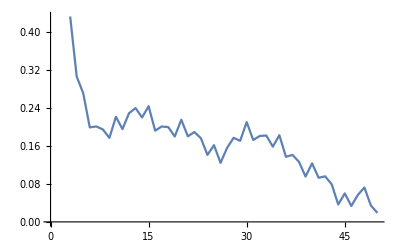

```mathematica
(*ListPlot[stats[[2,;;,1,1,1,1,1]],Joined->True]*)
ListPlot[Map[Mean,Transpose[stats[[2,;;,1,1,1,1,1]]]],Joined->True]
```

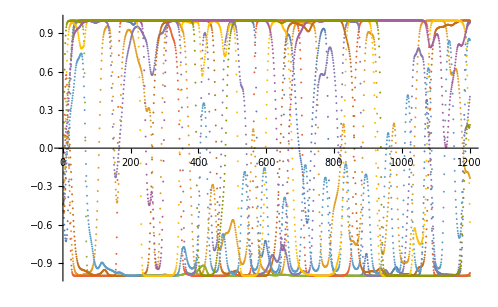

```mathematica
ListPlot[stats[[7,1;;10,1,1,1,1,1]]]
```

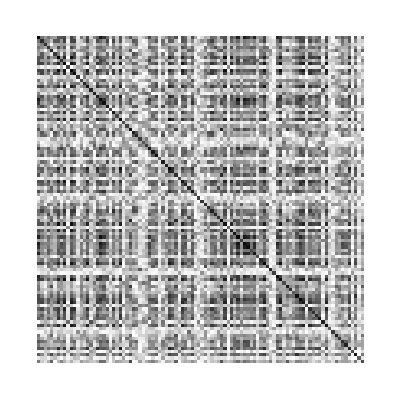
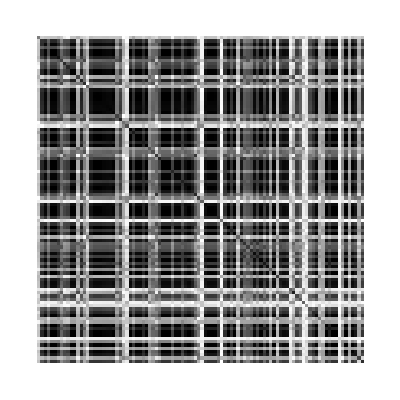
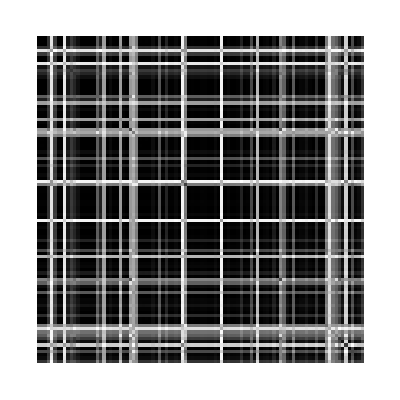
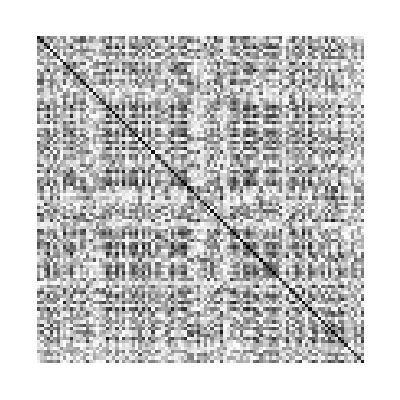
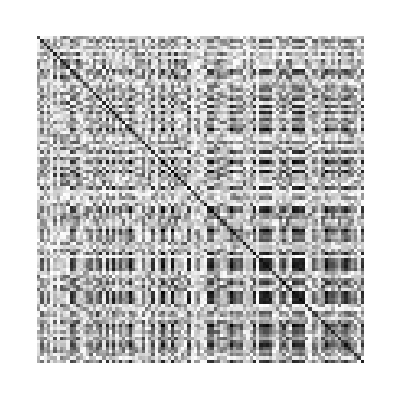
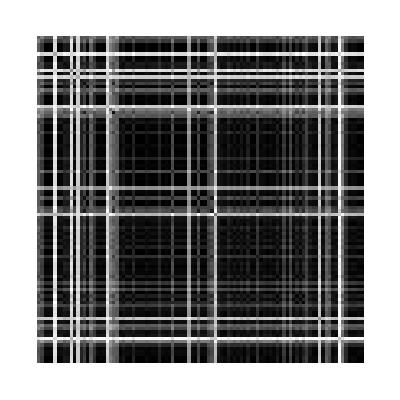
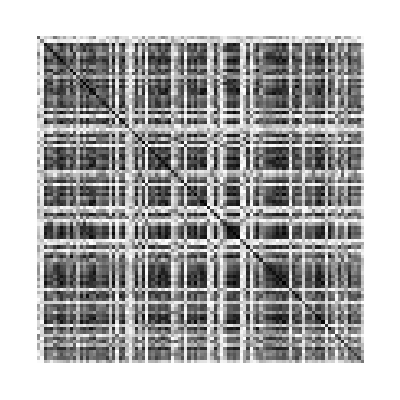
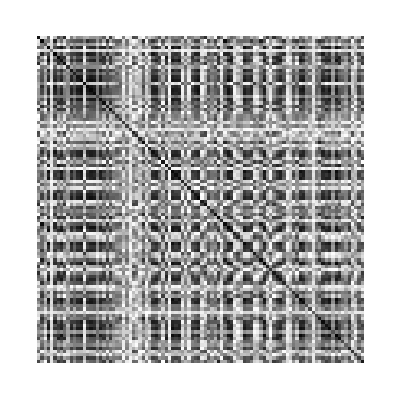

```mathematica
Map[ArrayPlot,stats[[3,1;;10,1,1,1,1,2]]]
```

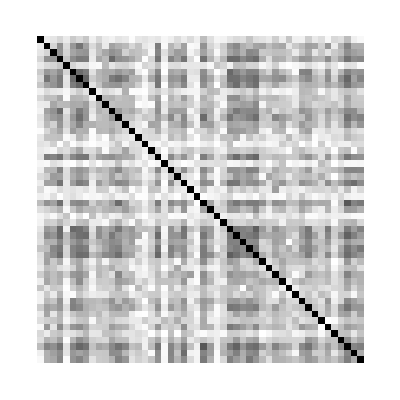
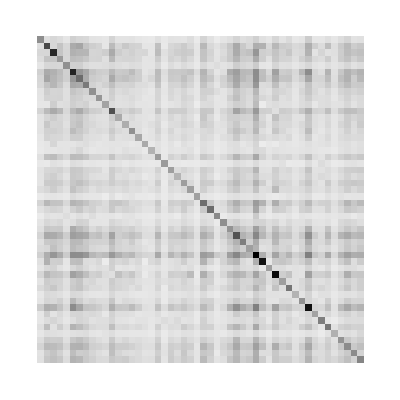

```mathematica
Table[ArrayPlot[Table[Table[fct[stats[[3,idx1,1,1,1,1,2]],stats[[3,idx2,1,1,1,1,2]]],{idx2,50}],{idx1,50}]],{fct,{firstPcSimilarity,overlapSimilarity}}]
```

```mathematica
Table[ListPlot3D[Table[Table[fct[stats[[3,idx1,1,1,1,1,2]],stats[[3,idx2,1,1,1,1,2]]],{idx2,50}],{idx1,50}]],{fct,{firstPcSimilarity,overlapSimilarity}}]
```

{-Graphics3D-,-Graphics3D-}